坐标变换-反序
三相静止坐标系ABC--两相静止坐标系αβ--两相旋转坐标系dq

1、三相静止坐标系ABC

220 √2 Cos[wt]

-220 √2 Sin[π/6+wt]

-220 √2 Sin[π/6-wt]

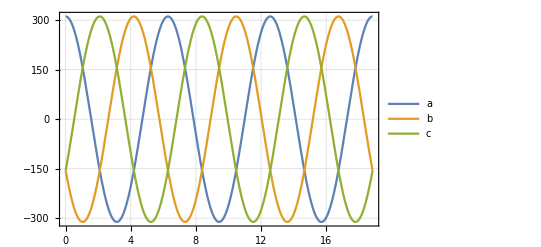

```mathematica
U = 220;
a=Sqrt[2]*U*Cos[-wt]
b=Sqrt[2]*U*Cos[-wt-2*Pi/3]
c=Sqrt[2]*U*Cos[-wt+2*Pi/3]
Plot[{a,b,c},{wt,0,6*Pi},Frame->True,GridLines->Automatic,PlotLegends->"Expressions"]
```

```mathematica
ABC={{a},{b},{c}};
MatrixForm[ABC]
```

(220 √2 Cos[wt]
-220 √2 Sin[π/6+wt]
-220 √2 Sin[π/6-wt])

## 2、三相静止坐标系ABC-两相静止坐标系αβ

Clark变换就是三相静止坐标系ABC到两相静止坐标系αβ的变换

        Clark变换有等功率变换和等幅值变换，二者只是系数不同。以下是等功率变换：
                                  [α
β]=√(2/3)[1 | -1/2 | -1/2
0 | (√3)/2 | -(√3)/2][a
b
c]

```mathematica
ABC2AB=Sqrt[2/3]*{{1,-1/2,-1/2},{0,Sqrt[3]/2,-Sqrt[3]/2}};
MatrixForm[ABC2AB]
```

(√(2/3) | -1/(√6) | -1/(√6)
0 | 1/(√2) | -1/(√2))

通过Clark变换（等功率）从ABC坐标系变换到αβ坐标系

```mathematica
AB=ABC2AB.ABC;
MatrixForm[AB]
```

((440 Cos[wt])/(√3)+(220 Sin[π/6-wt])/(√3)+(220 Sin[π/6+wt])/(√3)
220 Sin[π/6-wt]-220 Sin[π/6+wt])

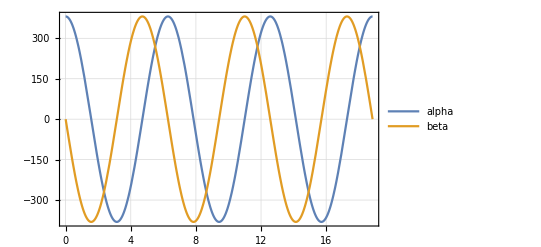

```mathematica
alpha=AB[[1,1]];
beta=AB[[2,1]];
Plot[{alpha,beta},{wt,0,6*Pi},Frame->True,GridLines->Automatic,PlotLegends->"Expressions"]
```

## 3、两相静止坐标系αβ-两相旋转坐标系dq

两相静止坐标系αβ到两相旋转坐标系的变换，φ是d轴和α轴之间的夹角

        变换如下
                                     [d
q]=[cosφ | sinφ
-sinφ | cosφ][α
β]

```mathematica
AB2DQ={{Cos[-wt],Sin[-wt]},{-Sin[-wt],Cos[-wt]}};
MatrixForm[AB2DQ]
```

(Cos[wt] | -Sin[wt]
Sin[wt] | Cos[wt])

```mathematica
DQ=AB2DQ.AB
```

{{-Sin[wt] (220 Sin[π/6-wt]-220 Sin[π/6+wt])+Cos[wt] ((440 Cos[wt])/(√3)+(220 Sin[π/6-wt])/(√3)+(220 Sin[π/6+wt])/(√3))},{Cos[wt] (220 Sin[π/6-wt]-220 Sin[π/6+wt])+Sin[wt] ((440 Cos[wt])/(√3)+(220 Sin[π/6-wt])/(√3)+(220 Sin[π/6+wt])/(√3))}}

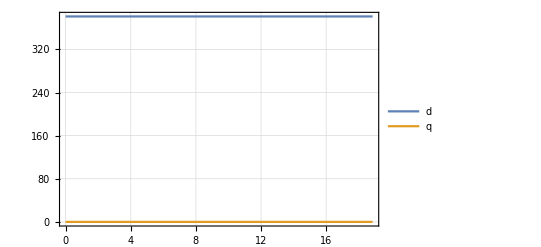

```mathematica
d=DQ[[1,1]];
q=DQ[[2,1]];
Plot[{d,q},{wt,0,6*Pi},Frame->True,GridLines->Automatic,PlotLegends->"Expressions"]
```

4、三相静止坐标系ABC到两相旋转坐标系dq的变换

三相静止坐标系ABC到两相旋转坐标系dq的变换如下

[d
q]=√(2/3)[cosφ | -1/2cosφ+(√3)/2 sinφ | -1/2cosφ-(√3)/2 sinφ
-sinφ | 1/2 sinφ+(√3)/2 cosφ | 1/2 sinφ-(√3)/2 cosφ][a
b
c]

5、两相静止坐标系αβ-三相静止坐标系ABC
        αβ坐标系变换为ABC坐标系，即三相静止变换为两相静止坐标系，称为逆Clark变换，下面是等功率逆Clark变换
                  [a
b
c]=√(2/3)[1 | 0
-1/2 | (√3)/2
-1/2 | -(√3)/2][α
β]

```mathematica
AB2ABC=Sqrt[2/3]*{{1,0},{-1/2,Sqrt[3]/2},{-1/2,-Sqrt[3]/2}};
MatrixForm[AB2ABC]
```

(√(2/3) | 0
-1/(√6) | 1/(√2)
-1/(√6) | -1/(√2))

```mathematica
ABC2=AB2ABC.AB;
MatrixForm[ABC2]
```

(√(2/3) ((440 Cos[wt])/(√3)+(220 Sin[π/6-wt])/(√3)+(220 Sin[π/6+wt])/(√3))
(220 Sin[π/6-wt]-220 Sin[π/6+wt])/(√2)-((440 Cos[wt])/(√3)+(220 Sin[π/6-wt])/(√3)+(220 Sin[π/6+wt])/(√3))/(√6)
-(220 Sin[π/6-wt]-220 Sin[π/6+wt])/(√2)-((440 Cos[wt])/(√3)+(220 Sin[π/6-wt])/(√3)+(220 Sin[π/6+wt])/(√3))/(√6))

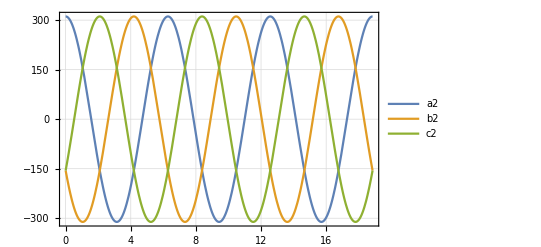

```mathematica
a2=ABC2[[1,1]];
b2=ABC2[[2,1]];
c2=ABC2[[3,1]];
Plot[{a2,b2,c2},{wt,0,6*Pi},Frame->True,GridLines->Automatic,PlotLegends->"Expressions"]
```

6、两相旋转坐标系dq-两相静止坐标系αβ
        两相旋转坐标系dq到两相静止坐标系αβ的变换，φ是d轴和α轴之间的夹角
        
                        [α
β]=[cosφ | -sinφ
sinφ | cosφ][d
q]